```mathematica
Clear["Global`*"]
```

```mathematica
TwoLayerMat[n_,r1_,r2_,ρ1_,ρ2_,η1_]:=Module[
{ν2,ν1,ηN,LL,ρN,Δρ,τrrc,τrra,M1,M2,M2f,M,g1,g2,MAT,RHS,A},
ν2=Log[r2/r1];
ν1=Log[r1/r1];
LL=n(n+1);
ηN=1;
ρ`N=1;
Δρ=ρ2-ρ1;
M1=ρ1 4/3 π r1^3;
M2=Δρ 4/3 π r2^3;
M2f=ρ2 4/3 π r2^3;
M=M1+M2;
g1=G M/r1^2;
g2=G M2f/r2^2;

A={{-2,LL,0,0},{-1,1,0,1/ηN},{12ηN,-6LL*ηN,1,LL},{-6ηN,2(2LL-1)ηN,-1,-2}};

PM=MatrixExp[A(ν1-ν2)]; 

(*define radial stresses on surface and CMB*)
τrra=(-ρ1 g1 h1[t]r1)/η1+(4π G ρ1)/((2n+1)η1) (r2^2(r2/r1)^n h2[t]Δρ+r1^2 h1[t]ρ1);
τrrc=(-Δρ g2 h2[t]r2)/η1+(Δρ/ρ1)(4π G ρ1 r2)/((2n+1)η1) (r2 h2[t]Δρ+r1(r2/r1)^n h1[t]ρ1);
(*write out the matrices equation*)
MAT={{1,0,-PM[[1,1]],-PM[[1,2]]},
   {0,1,-PM[[2,1]],-PM[[2,2]]},
   {0,0,-PM[[3,1]],-PM[[3,2]]},
   {0,0,-PM[[4,1]],-PM[[4,2]]}};
RHS=-Transpose[{{
PM[[1,3]]τrrc,
PM[[2,3]]τrrc,
PM[[3,3]]τrrc+τrra,
PM[[4,3]]τrrc
}}];
Return[{MAT,RHS}];
];
```

```mathematica
W[n_,r1_,r2_,ρ1_,ρ2_]:=Module[{MAT,RHS,DRHS,IC,deq,sol,h1evo,h2evo},
{MAT,RHS}=TwoLayerMat[n,r1,r2,ρ1,ρ2,10^24];
DRHS=LinearSolve[MAT/.G->6.67 10^-11,RHS/.G->6.67 10^-11]//Simplify;
IC={h1[0]==1000,h2[0]==0};
deq=Flatten@{h1'[t]==First@DRHS[[1]],h2'[t]==First@DRHS[[3]],IC};
sol=DSolve[deq,{h1[t],h2[t]},t];
h1evo=First@(h1[t]/.sol);
h2evo=First@(h2[t]/.sol);
Return[Abs@First@(h2evo/h1evo//FullSimplify)];
]
```

Solve the system of equations

```mathematica
{MAT,RHS}=TwoLayerMat[2,r1,r2,ρ1,ρ2,η1];
```

```mathematica
SECINYEAR=86400 365.2422;
```

```mathematica
nlist=Range[2,100,4];
```

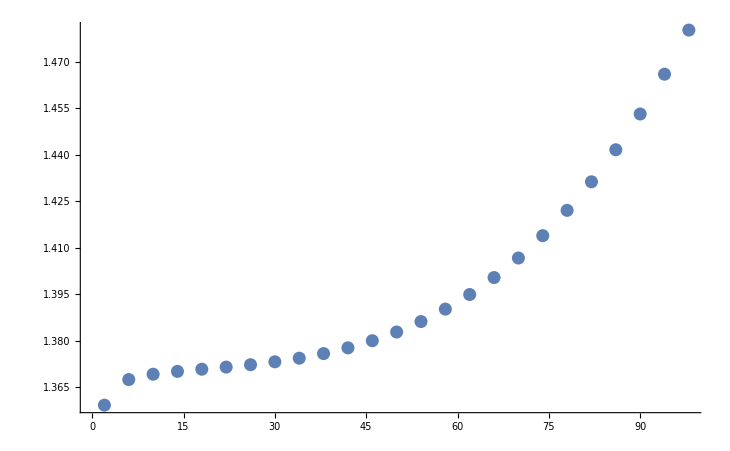

```mathematica
ListPlot[{nlist,(W[#,470000,460000,1400,2444])&/@nlist}//Transpose]
```

```mathematica
{MAT,RHS}=TwoLayerMat[2,470000,422330,1400,2444,1];
DRHS=LinearSolve[MAT/.G->6.67 10^-11,RHS/.G->6.67 10^-11]//Simplify;
IC={h1[0]==1000,h2[0]==0};
deq=Flatten@{h1'[t]==First@DRHS[[1]],h2'[t]==First@DRHS[[3]],IC};
sol=DSolve[deq,{h1[t],h2[t]},t];

h1evo=First@(h1[t]/.sol)//FullSimplify
h2evo=First@(h2[t]/.sol)//FullSimplify
```

583.527 ⅇ^(-5.58922×10^8 t)+416.473 ⅇ^(-2.03644×10^6 t)

606.334 ⅇ^(-5.58922×10^8 t)-606.334 ⅇ^(-2.03644×10^6 t)

```mathematica
(h2evo/h1evo)//FullSimplify
```

-1.52589+1/(0.389166+0.266189 ⅇ^(6.70781×10^7 t))